```mathematica
(*変数の初期化*)
ClearAll["Global`*"]
```

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

```mathematica
(*修正ブレットシュナイダー・光易型*)
S[H_,T_,f_]:=0.205*(H^2)*(T^-4)*(f^-5)*Exp[-0.75*(T*f)^-4];
```

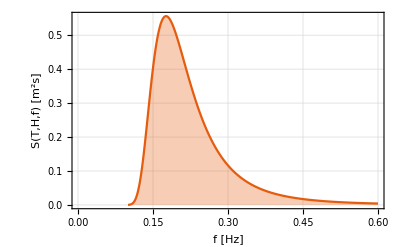

-Graphics3D-

```mathematica
(*有義波高と有義周期*)
H=1.;
T=5;
F=1/T;

(*プロット，またはサンプリングする範囲*)
minF=F/2;
maxF=3*F;

(*範囲を上のように調整すれば，スペクトル全体を常に表示できる*)
ListPlot[Table[{f,S[H,T,f]},{f,minF,maxF,0.001}]
,FrameLabel->{"f [Hz]","S(T,H,f) [m^2s]"}
,Evaluate[plot2Doption]
,GridLines->Automatic
,Filling->Bottom
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]

ListLinePlot3D[Table[{f,T,S[H,T,f]},{T,4,8,0.5},{f,0.5/T,3/T,0.01}]
,PlotRange->All
,Filling->Bottom
,Evaluate[plot3Doption]
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]
```

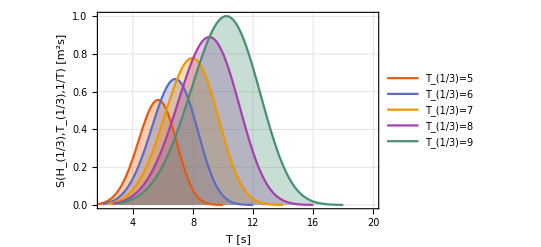

-Graphics3D-

```mathematica
(*範囲を上のように調整すれば，スペクトル全体を常に表示できる*)
ListPlot[Table[{1/f,S[H,T,f]},{T,5,9,1},{f,(1/T)/2,(3/T),0.001}]
,FrameLabel->{"T [s]","S(H_(1/3),T_(1/3),1/T) [m^2s]"}
,PlotRange->{{2,20},All}
,Evaluate[plot2Doption]
,GridLines->Automatic
,Filling->Bottom
,PlotLegends->Table["T_(1/3)="<>ToString[i],{i,5,9}]
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]

ListLinePlot3D[Table[{1/f,T,S[H,T,f]},{T,4,8,0.5},{f,0.5/T,3/T,0.01}]
,PlotRange->All
,Filling->Bottom
,Evaluate[plot3Doption]
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]
```

## スペクトルから有義波を計算する

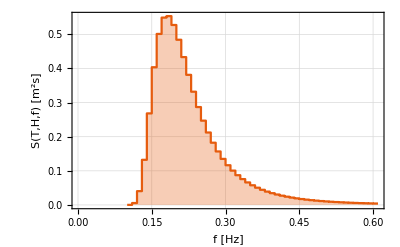

```mathematica
h=100;
g=9.81;

(*分散関係式*)
DispersionRelation[w_]:=k/.FindRoot[w^2==g*k*Tanh[k*h],{k,w^2/g}];

n=50;(*分割数*)
df=(maxF-minF)/n;(*スペクトルの分割刻み*)

ListStepPlot[Table[{minF+df*i,S[H,T,minF+df*i]},{i,0,n}]
,FrameLabel->{"f [Hz]","S(T,H,f) [m^2s]"}
,Evaluate[plot2Doption]
,GridLines->Automatic
,Filling->Bottom
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]
wave[x_,t_]=Quiet@Sum[Module[{f,w,k,a,theta},
f=minF+df*i;
w=2*π*f;
k=DispersionRelation[w];
a=Sqrt[2*S[H,T,f]*df];(*波の成分の振幅は，Sを使ってこれで求まるはず m^2*s=S[H,T,f]*)
theta=RandomReal[{0,2 π}];(*波の各成分の位相のずれはランダム*)
a*Cos[k*x-w*t+theta]],{i,0,n}];
```

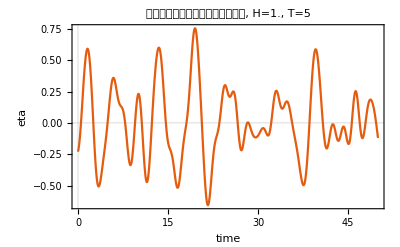

```mathematica
x=0.;
ListPlot[Table[{t,wave[x,t]},{t,0,10.*T,0.01*T}]
,Evaluate[plot2Doption]
,PlotTheme->"Scientific"
,PlotLabel->StringJoin["スペクトルから計算した不規則波, ","H=",ToString[H],", T=",ToString[T]]
,FrameLabel->{"time","eta"}
]
```

## 出力波形から有義波高と有義周期をゼロアップクロス法を使って計算

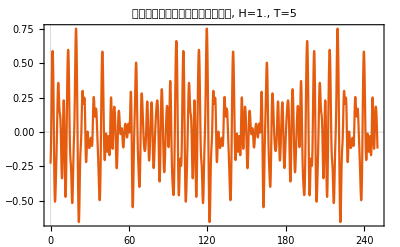

```mathematica
(*Generate wave data*)
data=Table[{t,wave[x,t]},{t,0,50.*T,0.01*T}];

ListPlot[data
,Evaluate[plot2Doption]
,PlotLabel->StringJoin["スペクトルから計算した不規則波, ","H=",ToString[H],", T=",ToString[T]]]
```

{10,99,191,247,362,472,565,644,772,913,959,1031,1079,1130,1180,1209,1281,1379,1462,1527,1601,1685,1763,1815,1901,2010,2099,2191,2247,2362,2472,2565,2644,2772,2913,2959,3031,3079,3130,3180,3209,3281,3379,3462,3527,3601,3685,3763,3815,3901,4010,4099,4191,4247,4362,4472,4565,4644,4772,4913,4959}

{52,158,213,293,413,533,569,714,817,940,994,1067,1096,1160,1205,1241,1330,1421,1494,1561,1651,1721,1797,1848,1947,2052,2158,2213,2293,2413,2533,2569,2714,2817,2940,2994,3067,3096,3160,3205,3241,3330,3421,3494,3561,3651,3721,3797,3848,3947,4052,4158,4213,4293,4413,4533,4569,4714,4817,4940,4994}

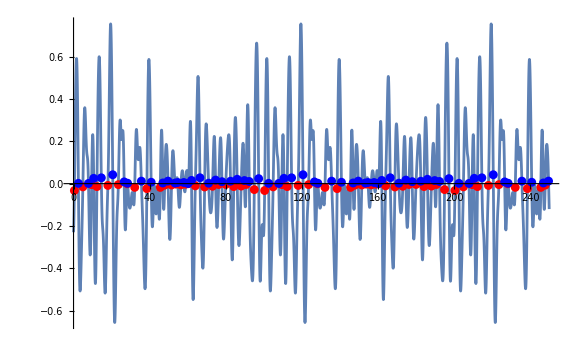

```mathematica
(*ゼロアップクロス点．これを使う*)
zeroUpCrossings=DeleteCases[Table[If[data[[i,2]]*data[[i+1,2]]<0&&data[[i,2]]<0&&data[[i+1,2]]>0,i],{i,1,Length[data]-1}],Null]
(*ゼロダウンクロス点*)
zeroDownCrossings=DeleteCases[Table[If[data[[i,2]]*data[[i+1,2]]<0&&data[[i,2]]>0&&data[[i+1,2]]<0,i],{i,1,Length[data]-1}],Null]

Show[
ListPlot[data,Joined->True],
ListPlot[Table[data[[i]],{i,zeroUpCrossings}],PlotStyle->Red],
ListPlot[Table[data[[i]],{i,zeroDownCrossings}],PlotStyle->Blue]]
```

```mathematica
(*Compute wave heights and periods*)waveHeights=Table[(*Find the peak after the current zero up-crossing and the trough before the next one*)dataSubset=data[[zeroUpCrossings[[i]];;zeroUpCrossings[[i+1]]]];
peak=Max[dataSubset[[All,2]]];
trough=Min[dataSubset[[All,2]]];
(*Compute the wave height as the difference between the peak and the trough*)
peak-trough,{i,1,Length[zeroUpCrossings]-1}]

wavePeriods=(data[[zeroUpCrossings[[#+1]],1]]-data[[zeroUpCrossings[[#]],1]])&/@Range[1,Length[zeroUpCrossings]-1]

(*Compute significant wave height and period*)
significantWaveHeight=Mean[Sort[waveHeights,Greater][[1;;Round[Length[waveHeights]/3]]]];
significantWavePeriod=Mean[Sort[wavePeriods,Greater][[1;;Round[Length[wavePeriods]/3]]]];

Print["有義波高 ",significantWaveHeight]
Print["有義周期 ",significantWavePeriod]
```

{1.09827,0.6961,0.703573,1.1168,1.41059,0.519716,0.119987,0.753069,0.791006,0.374652,0.449323,0.170686,0.140848,0.100035,0.0652376,0.842024,0.905783,0.42062,0.430801,0.479319,0.591627,0.605709,0.30056,0.83226,1.12517,1.09827,0.6961,0.703573,1.1168,1.41059,0.519716,0.119987,0.753069,0.791006,0.374652,0.449323,0.170686,0.140848,0.100035,0.0652376,0.842024,0.905783,0.42062,0.430801,0.479319,0.591627,0.605709,0.30056,0.83226,1.12517,1.09827,0.6961,0.703573,1.1168,1.41059,0.519716,0.119987,0.753069,0.791006,0.374652}

{4.45,4.6,2.8,5.75,5.5,4.65,3.95,6.4,7.05,2.3,3.6,2.4,2.55,2.5,1.45,3.6,4.9,4.15,3.25,3.7,4.2,3.9,2.6,4.3,5.45,4.45,4.6,2.8,5.75,5.5,4.65,3.95,6.4,7.05,2.3,3.6,2.4,2.55,2.5,1.45,3.6,4.9,4.15,3.25,3.7,4.2,3.9,2.6,4.3,5.45,4.45,4.6,2.8,5.75,5.5,4.65,3.95,6.4,7.05,2.3}

有義波高 1.03302

有義周期 5.6675